# Polynomial fitting

Curve fitting means approximating points by curves.

A curve might be complex enough that finding its exact polynomial might be too difficult. Instead, a similar enough curve can be found from samples of the original curve that give sufficient precision solutions to a problem.

A polynomial curve might have enough inflection points, that is, a high enough degree, to mimic the shape to another curve. Then, the coefficients of each term can be adjusted.

One technique for finding coefficients is simply checking the candidate curve at the sample points against the sample points and taking the absolute difference.

If the absolute differences at each point are summed in squares, for example

f(a,b,c,d,e)=0.1 a^2+0.3 b^2-0.4 c^2+0.21 d^2-0.05 e^2,

where 0.1, 0.3, -0.4, 0.21, -0.05 are the differences, then the sum that yields zero or the lowest value in absolute, that is, the minimum of the function, is the best fit curve.

This can be found, through calculus, by setting the partial derivative of each variable to zero and solving a resulting system of equations in equal number of variables giving the best value for each variable.

The below curve is a degree 7 polynomial and the points are an 8-point series.
The black dots are sample points and the blue line is the solution.

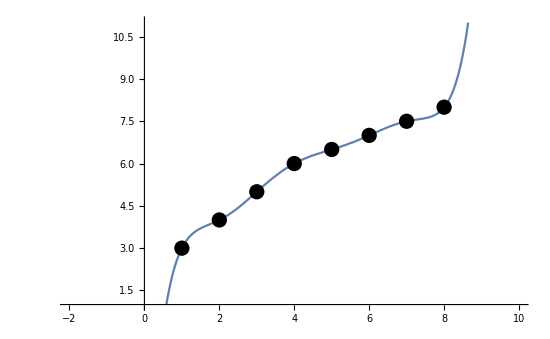

```mathematica
t={1,2,3,4,5,6,7,8};
v={3,4,5,6,6.5,7,7.5,8};
ts=TimeSeries[v,{t}];
fp7[x_, a7_,a6_,a5_,a4_,a3_,a2_,a1_,a0_]:=a7*x^7+a6*x^6+a5*x^5+a4*x^4+a3*x^3+a2*x^2+a1*x^1+a0*x^0
Show[Plot[fp7[x,0.00099206,-0.03194444,0.41944444,-2.88194445,11.04861112,-23.33611114,25.78095241,-8.00000001],{x,-2,10},PlotRange->{{-2,10},{1,11}},ImageSize->550],
ListPlot[ts, PlotStyle->{PointSize[.02],Black}]]
```

The below plot is a 10-point series and the corresponding polynomial fits from degree 1 through 10.
The markings in the legends show the degree of each polynomial (“pol1”, “pol2”, etc.).

These polynomials are of the form

x^n+x^(n-1)+…+x^0, for degree n.
That is, they contain all lesser degree terms (with unitary coefficients).
For example, the degree 6 polynomial is:

x^6+x^5+x^4+x^3+x^2+x^1+x^0

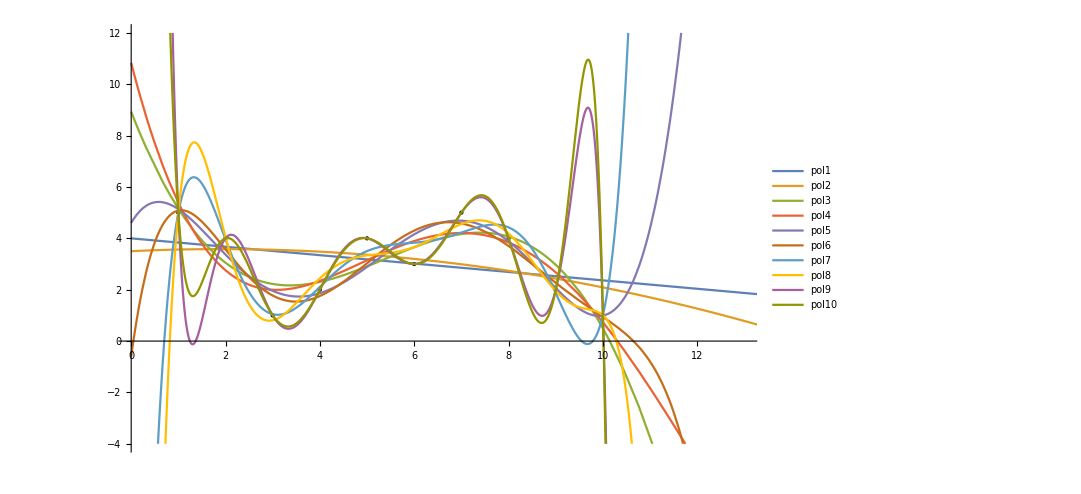

```mathematica
Block[{data,pol1,pol2,pol3,pol4,pol5,pol6,pol7,pol8,pol9,pol10},
data={5,4,1,2,4,3,5,4,2,1};
pol1=Fit[data,{1,x},x];
pol2=Fit[data,{1,x,x^2},x];
pol3=Fit[data,{1,x,x^2,x^3},x];
pol4=Fit[data,{1,x,x^2,x^3,x^4},x];
pol5=Fit[data,{1,x,x^2,x^3,x^4,x^5},x];
pol6=Fit[data,{1,x,x^2,x^3,x^4,x^5,x^6},x];
pol7=Fit[data,{1,x,x^2,x^3,x^4,x^5,x^6,x^7},x];
pol8=Fit[data,{1,x,x^2,x^3,x^4,x^5,x^6,x^7,x^8},x];
pol9=Fit[data,{1,x,x^2,x^3,x^4,x^5,x^6,x^7,x^8,x^9},x];
pol10=Fit[data,{1,x,x^2,x^3,x^4,x^5,x^6,x^7,x^8,x^9,x^10},x];
Show[ListPlot[PadRight[data,13,20],PlotStyle->Directive[PointSize->.02,Black],PlotRange->{-4,12},ImageSize->800],Plot[{pol1,pol2,pol3,pol4,pol5,pol6,pol7,pol8,pol9,pol10},{x,0,16},PlotRange->{-4,12},PlotLegends->"Expressions"]]
]
```

The graph shows higher degree polynomials provide more opportunity for a detailed fit through the points (by adjusting more coefficients). This also shows the asymptotes (continuations to the infinite) present in each curve.

Let’s generate the fits for polynomials of the form

x^n, for degree n.
That is, they contain no lesser degree terms (with unitary coefficients).
For example, the degree 6 polynomial is:

x^6

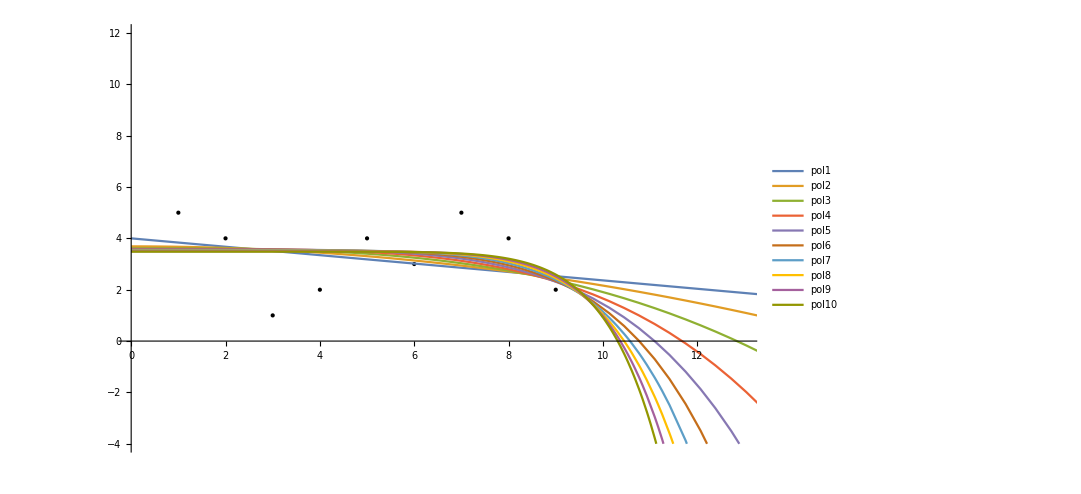

```mathematica
Block[{data,pol1,pol2,pol3,pol4,pol5,pol6,pol7,pol8,pol9,pol10},
data={5,4,1,2,4,3,5,4,2,1};
pol1=Fit[data,{1,x},x];
pol2=Fit[data,{1,x^2},x];
pol3=Fit[data,{1,x^3},x];
pol4=Fit[data,{1,x^4},x];
pol5=Fit[data,{1,x^5},x];
pol6=Fit[data,{1,x^6},x];
pol7=Fit[data,{1,x^7},x];
pol8=Fit[data,{1,x^8},x];
pol9=Fit[data,{1,x^9},x];
pol10=Fit[data,{1,x^10},x];
Show[ListPlot[PadRight[data,13,-100],PlotStyle->Directive[PointSize->.02,Black],PlotRange->{-4,12},ImageSize->800],Plot[{pol1,pol2,pol3,pol4,pol5,pol6,pol7,pol8,pol9,pol10},{x,0,16},PlotRange->{-4,12},PlotLegends->"Expressions"]]
]
```

The closer the coefficients of the terms of the polynomial are to zero, the less detail the polynomial features.
Still, each degree polynomial possesses a distinct asymptote.

Each higher degree of polynomial has faster asymptotes.

In the below example, because of the low number of points, the parabola’s asymptote makes it inadequate for prediction. The line is the only possible prediction curve.

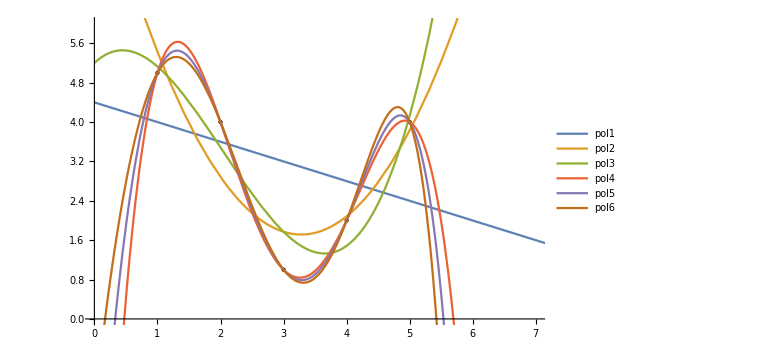

```mathematica
Block[{data,pol1,pol2,pol3,pol4,pol5,pol6},
data={5,4,1,2,4};
pol1=Fit[data,{1,x},x];
pol2=Fit[data,{1,x,x^2},x];
pol3=Fit[data,{1,x,x^2,x^3},x];
pol4=Fit[data,{1,x,x^2,x^3,x^4},x];
pol5=Fit[data,{1,x,x^2,x^3,x^4,x^5},x];
pol6=Fit[data,{1,x,x^2,x^3,x^4,x^5,x^6},x];
Show[ListPlot[PadRight[data,7,-1],PlotStyle->Directive[PointSize->.03,Black],PlotRange->{0,6},(*DataRange->{0,5},*)ImageSize->Large],Plot[{pol1,pol2,pol3,pol4,pol5,pol6},{x,0,10},PlotLegends->"Expressions"]]
]
```

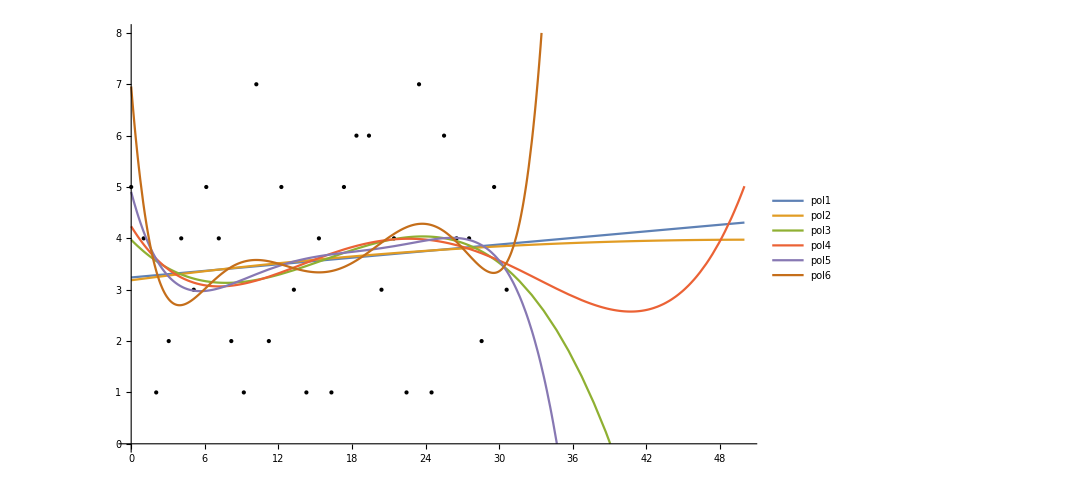

```mathematica
Block[{data,pol1,pol2,pol3,pol4,pol5,pol6,pol7,pol8,pol9,pol10},
data={5,4,1,2,4,3,5,4,2,1,7,2,5,3,1,4,1,5,6,6,3,4,1,7,1,6,4,4,2,5,3};
pol1=Fit[data,{1,x},x];
pol2=Fit[data,{1,x,x^2},x];
pol3=Fit[data,{1,x,x^2,x^3},x];
pol4=Fit[data,{1,x,x^2,x^3,x^4},x];
pol5=Fit[data,{1,x,x^2,x^3,x^4,x^5},x];
pol6=Fit[data,{1,x,x^2,x^3,x^4,x^5,x^6},x];
Show[ListPlot[PadRight[data,50,10],PlotStyle->Directive[PointSize->.01,Black],PlotRange->{0,8},DataRange->{0,50},ImageSize->800],Plot[{pol1,pol2,pol3,pol4,pol5,pol6},{x,0,50},PlotRange->{0,8},ImageSize->800,PlotLegends->"Expressions"]]
]
```

Let’s observe a point series with a higher number of points.

In this example, only the line and parabola are appropriate for prediction, next to the ending point. The other polynomials feature sharp asymptotes making predictions innacurate.